```mathematica
experiments={
"EYrainbow_glucose",
"EYrainbow_glucose_largerBF",
"EYrainbow_rapamycin_1stTry",
"EYrainbow_rapamycin_CheckBistability",
"EYrainbow_1nmpp1_1st",
"EYrainbow_leucine_large",
"EYrainbowWhi5Up_betaEstrodiol"
};
data = Import[FileNameJoin[{NotebookDirectory[],"fitCellSizeWithOrganelle.csv"}],"Data","HeaderLines"->1];
epsilon = 10^(-18);
filled = data/.{0.->epsilon};
washed = Select[data,Function[x,NoneTrue[x,#==0&]]];
```

```mathematica
(* Check data *)
Position[filled,0.]
Position[washed,0.]
```

{}

{}

```mathematica
Length[filled]
Length[washed]
```

43108

29263

```mathematica
fitCellSizeFromOrganelles[dataset_]:=Module[
{expr,a,b,c,alpha,mean,n,nlm,params,fittedFunc,fitted,fittedMin,fittedMax,dataMin,dataMax},
expr = Sum[a[i]n[i]mean[i]^alpha[i],{i,1,6}]+Sum[n[i]mean[i]^alpha[i]b[i,j]n[j]mean[j]^alpha[j],{i,1,5},{j,i+1,6}]+c;
nlm = NonlinearModelFit[
dataset[[All,2;;]],expr,
Join[
Table[a[i],{i,1,6}],
Flatten[Table[b[i,j],{i,1,5},{j,i+1,6}]],
{c},
Table[alpha[i],{i,1,6}]
],
Join[
Table[mean[i],{i,1,6}],
Table[n[i],{i,1,6}]
],
MaxIterations->∞
];
params=nlm["BestFitParameters"];
Print["a[i]: ",Table[a[i],{i,1,6}]/.params];
Print["b[i,j]: ",Table[b[i,j],{i,1,6},{j,1,6}]/.params//MatrixForm];
Print["c: ", c/.params];
Print["alpha[i]: ",Table[alpha[i],{i,1,6}]/.params];
Print["Adjusted R Square: ", nlm["AdjustedRSquared"]];
Print["p-values for parameter z-statistics: ", nlm["ParameterPValues"]];
Print["t-statistics for parameter estimates: ", nlm["ParameterTStatistics"]];
fittedFunc = Function[
vec,
expr/.params
/.Table[n[i]->vec[[i]],{i,1,6}]
/.Table[mean[i]->vec[[i+6]],{i,1,6}]
];
fitted = Map[fittedFunc,dataset[[All,2;;-2]]];
fittedMin = Min[fitted];
fittedMax = Max[fitted];
dataMin = Min[dataset[[All,-1]]];
dataMax = Max[dataset[[All,-1]]];
Print[Show[
ListPlot[
Transpose[{dataset[[All,-1]],fitted}],
PlotTheme->"Scientific",AspectRatio->(fittedMax)/(dataMax)
],
Plot[x,{x,0,dataMax}]
]];
Print[""]
]
```

All Experiments, Null Organelles filled with 0:

a[i]: {6.49774,0.267067,0.166206,0.311544,1.52843,-5.64473}

b[i,j]: (b$6141[1,1] | 0.00465407 | -0.00103422 | -0.0128998 | 0.0217947 | 0.029648
b$6141[2,1] | b$6141[2,2] | 0.000010672 | -0.00123349 | -0.00116618 | -0.00354855
b$6141[3,1] | b$6141[3,2] | b$6141[3,3] | 0.000701859 | -0.000307819 | -0.00179042
b$6141[4,1] | b$6141[4,2] | b$6141[4,3] | b$6141[4,4] | 0.016488 | -0.0700616
b$6141[5,1] | b$6141[5,2] | b$6141[5,3] | b$6141[5,4] | b$6141[5,5] | 0.202412
b$6141[6,1] | b$6141[6,2] | b$6141[6,3] | b$6141[6,4] | b$6141[6,5] | b$6141[6,6])

c: 55.2923

alpha[i]: {0.821002,1.23737,1.81746,-0.494198,0.706441,0.827913}

Adjusted R Square: 0.936439

p-values for parameter z-statistics: {7.4503×10^-219,1.16162×10^-31,1.33233×10^-31,0.0000108475,1.0892×10^-66,1.25516×10^-190,2.23406×10^-17,3.9629×10^-14,0.0261587,0.0114705,0.036038,1.7077×10^-6,1.12297×10^-11,2.67×10^-13,4.13756×10^-15,1.61135×10^-16,9.93064×10^-9,2.76844×10^-20,4.93877×10^-7,9.49005×10^-26,7.46483×10^-200,0.,0.,0.,0.,6.75925×10^-20,0.,3.83922×10^-318}

t-statistics for parameter estimates: {31.7616,11.7173,11.7056,4.40007,17.2815,-29.5991,8.48452,-7.56476,-2.22392,2.52814,2.09656,4.78592,-6.79165,-7.31238,-7.85354,8.25125,-5.73304,-9.23218,5.02944,-10.4979,30.3221,40.4577,54.8683,80.141,87.1351,-9.13592,152.345,38.4558}

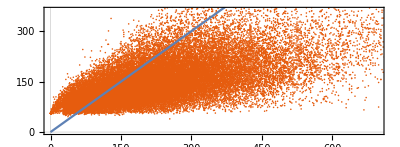

```mathematica
Print["All Experiments, Null Organelles filled with 0:"];
fitCellSizeFromOrganelles[filled]
```

All Experiments, Null Organelles Excluded:

a[i]: {7.27632,0.637428,0.111243,-0.0408166,2.75319,-2.15766}

b[i,j]: (b$6839[1,1] | 0.00872559 | 0.00041607 | 0.0765418 | -0.117424 | -0.0158225
b$6839[2,1] | b$6839[2,2] | -0.0000762617 | -0.00225043 | -0.00287057 | 0.000057378
b$6839[3,1] | b$6839[3,2] | b$6839[3,3] | -0.000110451 | 0.000833496 | -0.000802602
b$6839[4,1] | b$6839[4,2] | b$6839[4,3] | b$6839[4,4] | 0.0327809 | -0.0647805
b$6839[5,1] | b$6839[5,2] | b$6839[5,3] | b$6839[5,4] | b$6839[5,5] | 0.0691652
b$6839[6,1] | b$6839[6,2] | b$6839[6,3] | b$6839[6,4] | b$6839[6,5] | b$6839[6,6])

c: 29.0454

alpha[i]: {0.91547,1.12851,1.80627,-0.273857,0.714294,0.985525}

Adjusted R Square: 0.954803

p-values for parameter z-statistics: {2.06651×10^-163,2.8714×10^-43,5.17943×10^-12,0.690175,7.86805×10^-121,2.10436×10^-23,8.08621×10^-17,0.0122275,1.71779×10^-18,1.03514×10^-25,0.297465,3.37554×10^-8,7.33548×10^-9,3.74157×10^-16,0.919289,0.119744,0.0000688879,6.19121×10^-6,1.39214×10^-10,1.57966×10^-15,6.15888×10^-20,1.85115×10^-43,0.,0.,0.,5.48457×10^-6,0.,2.33676×10^-106}

t-statistics for parameter estimates: {27.4161,13.814,6.90344,-0.398622,23.4838,-9.97656,8.33499,2.50567,8.78028,-10.4929,-1.0419,-5.52224,-5.78476,-8.15134,0.10133,-1.5559,3.98067,-4.52058,6.41907,-7.97495,9.14812,13.8458,55.9065,81.012,47.6296,-4.54619,147.712,21.9952}

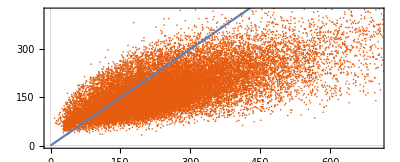

```mathematica
Print["All Experiments, Null Organelles Excluded:"];
fitCellSizeFromOrganelles[washed];
```

EYrainbow_glucose, Null Organelles filled with 0:

a[i]: {1.96285,0.0613439,0.0640699,4.54943,7.51757,-0.0369611}

b[i,j]: (b$7320[1,1] | -0.000384568 | -0.000968002 | -0.116933 | 0.972618 | -0.0303605
b$7320[2,1] | b$7320[2,2] | -3.83656×10^-6 | 0.000910429 | -0.000954013 | 0.0000485664
b$7320[3,1] | b$7320[3,2] | b$7320[3,3] | 0.000891228 | -0.000131898 | -0.0000528637
b$7320[4,1] | b$7320[4,2] | b$7320[4,3] | b$7320[4,4] | -0.947297 | 0.0101995
b$7320[5,1] | b$7320[5,2] | b$7320[5,3] | b$7320[5,4] | b$7320[5,5] | 0.00825635
b$7320[6,1] | b$7320[6,2] | b$7320[6,3] | b$7320[6,4] | b$7320[6,5] | b$7320[6,6])

c: 11.0702

alpha[i]: {0.382693,1.53313,2.22198,0.60163,0.346872,-0.888535}

Adjusted R Square: 0.9241

p-values for parameter z-statistics: {0.00121458,0.000140243,1.31383×10^-9,1.41021×10^-9,9.87911×10^-24,0.65291,0.0534273,0.0000852291,0.0838691,1.12048×10^-29,0.00750272,0.00215092,0.00323543,0.000662374,0.0881014,0.000057822,0.467977,0.0341015,4.81296×10^-19,0.268258,0.397075,0.00162995,2.74904×10^-16,3.14423×10^-202,0.,1.22704×10^-9,6.08127×10^-81,7.90733×10^-12}

t-statistics for parameter estimates: {3.23684,3.80998,6.0744,6.06296,10.0818,-0.449744,-1.9318,-3.93165,-1.72893,11.3694,-2.67449,-3.06977,2.94552,-3.40632,1.70575,4.02415,-0.725816,-2.11931,-8.94378,1.10718,0.846911,3.1518,8.205,31.4346,54.616,6.08542,19.3201,-6.85263}

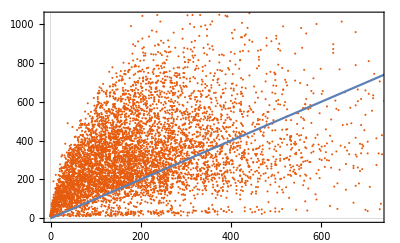

EYrainbow_glucose_largerBF, Null Organelles filled with 0:

a[i]: {27.7632,0.209062,-98.9008,-75.1794,11.8814,-9.2423}

b[i,j]: (b$7467[1,1] | 0.000402422 | -17.3051 | 0.399863 | 0.00190061 | -0.170456
b$7467[2,1] | b$7467[2,2] | -0.0493004 | -0.000269191 | -0.00179945 | 0.000449071
b$7467[3,1] | b$7467[3,2] | b$7467[3,3] | 59.6647 | -5.54589 | 3.36511
b$7467[4,1] | b$7467[4,2] | b$7467[4,3] | b$7467[4,4] | 0.158141 | -0.268734
b$7467[5,1] | b$7467[5,2] | b$7467[5,3] | b$7467[5,4] | b$7467[5,5] | 0.087516
b$7467[6,1] | b$7467[6,2] | b$7467[6,3] | b$7467[6,4] | b$7467[6,5] | b$7467[6,6])

c: 158.874

alpha[i]: {1.26309,1.57268,0.0830756,0.780118,0.775358,0.453073}

Adjusted R Square: 0.941201

p-values for parameter z-statistics: {1.79899×10^-11,0.0000266879,5.52483×10^-45,5.26356×10^-21,6.38773×10^-17,0.0000532302,0.390246,1.91321×10^-6,0.0000407317,0.973001,0.00934973,0.0146395,0.443983,0.0000438192,0.0302883,2.03128×10^-14,5.44435×10^-6,0.0707762,2.64832×10^-6,2.07715×10^-12,5.42001×10^-23,3.03209×10^-109,1.51705×10^-43,2.56639×10^-199,3.16911×10^-13,4.65366×10^-68,0.,1.24325×10^-70}

t-statistics for parameter estimates: {6.73452,4.20332,-14.1919,-9.43918,8.38275,-4.04391,0.859233,-4.76712,4.10636,0.0338461,-2.59984,-2.44189,-0.765536,-4.0894,2.16682,7.66777,-4.55103,1.80723,4.70091,-7.0441,9.91452,22.674,13.9499,31.3064,7.30358,17.6582,105.155,18.0071}

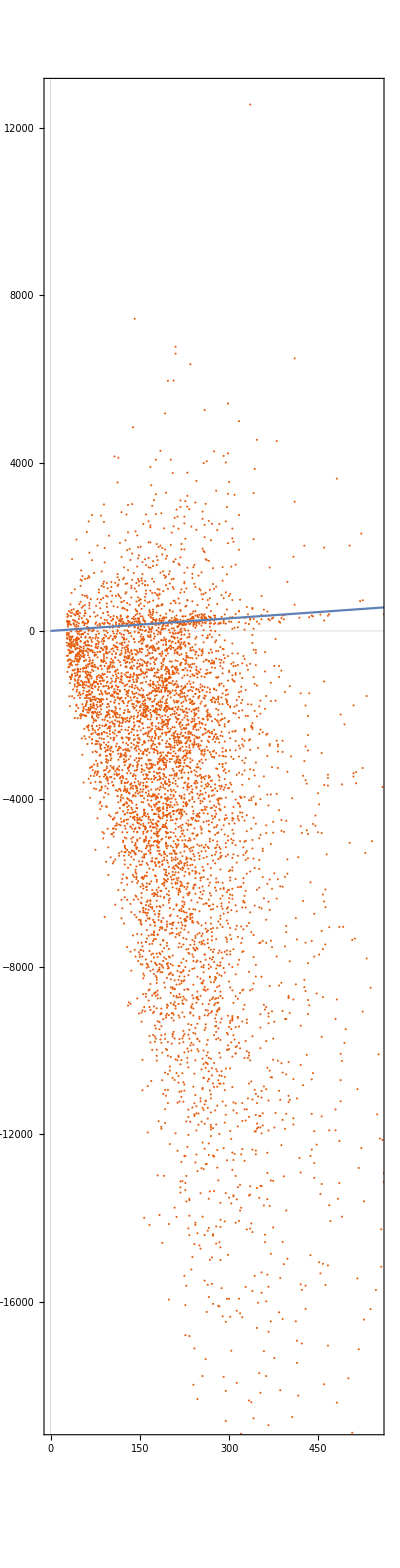

EYrainbow_rapamycin_1stTry, Null Organelles filled with 0:

a[i]: {5.65461,0.000175056,0.183508,-5.66655,5.39667,-7.14864}

b[i,j]: (b$7613[1,1] | -3.87351×10^-6 | -0.00144402 | -0.110238 | -0.00312312 | 0.060145
b$7613[2,1] | b$7613[2,2] | -4.74079×10^-10 | 5.71721×10^-6 | -2.98542×10^-6 | 1.10449×10^-6
b$7613[3,1] | b$7613[3,2] | b$7613[3,3] | 0.0011629 | 0.0000993934 | -0.00121016
b$7613[4,1] | b$7613[4,2] | b$7613[4,3] | b$7613[4,4] | -0.0702207 | 0.194071
b$7613[5,1] | b$7613[5,2] | b$7613[5,3] | b$7613[5,4] | b$7613[5,5] | 0.101518
b$7613[6,1] | b$7613[6,2] | b$7613[6,3] | b$7613[6,4] | b$7613[6,5] | b$7613[6,6])

c: 52.8359

alpha[i]: {0.460394,2.67942,1.75766,1.58509,0.78282,0.597937}

Adjusted R Square: 0.958456

p-values for parameter z-statistics: {4.45134×10^-14,0.210564,0.0000619644,2.17203×10^-16,1.01978×10^-90,1.00516×10^-44,0.203217,0.158517,0.248284,0.935731,0.293148,0.941586,0.222922,0.21896,0.308426,0.143421,0.751483,0.0395392,0.0361645,0.0000664945,5.98042×10^-10,3.48158×10^-69,2.91866×10^-16,1.44527×10^-64,6.83273×10^-175,2.74371×10^-63,0.,2.49901×10^-29}

t-statistics for parameter estimates: {7.56263,1.25213,4.00763,-8.23218,20.4948,-14.1303,-1.27256,-1.41023,-1.15462,-0.0806394,1.05132,-0.0732787,1.2189,-1.22941,1.0186,1.46333,0.316697,-2.05891,-2.09547,3.99089,6.1996,17.7757,8.19638,17.1423,29.0103,16.9632,108.44,11.2943}

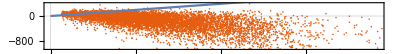

EYrainbow_rapamycin_CheckBistability, Null Organelles filled with 0:

a[i]: {1.70957,0.261828,0.185392,0.71068,0.869857,-2.24281}

b[i,j]: (b$7751[1,1] | 0.000112127 | -0.00135973 | -0.0203925 | 0.0990519 | 0.0339313
b$7751[2,1] | b$7751[2,2] | -0.0000850057 | 0.000189132 | -0.00161657 | -0.00145842
b$7751[3,1] | b$7751[3,2] | b$7751[3,3] | 0.000872282 | 0.000591907 | 0.000360483
b$7751[4,1] | b$7751[4,2] | b$7751[4,3] | b$7751[4,4] | -0.0204473 | -0.00992882
b$7751[5,1] | b$7751[5,2] | b$7751[5,3] | b$7751[5,4] | b$7751[5,5] | 0.0470586
b$7751[6,1] | b$7751[6,2] | b$7751[6,3] | b$7751[6,4] | b$7751[6,5] | b$7751[6,6])

c: 49.262

alpha[i]: {0.860968,1.42371,1.74564,-0.862589,0.851399,1.5064}

Adjusted R Square: 0.963717

p-values for parameter z-statistics: {0.000034518,4.25424×10^-9,0.0000680773,1.2893×10^-9,2.66615×10^-8,1.01258×10^-10,0.801888,0.0329196,0.00865992,3.66071×10^-8,0.173467,0.00357657,0.184429,0.0000133868,0.007426,0.0191808,0.0854975,0.555358,5.60758×10^-6,0.0933503,0.000256487,3.61022×10^-84,1.44556×10^-171,1.41939×10^-305,5.42247×10^-128,4.7558×10^-30,0.,3.02381×10^-9}

t-statistics for parameter estimates: {4.14343,5.8796,3.98471,6.07489,5.56683,-6.4725,0.250911,-2.13338,-2.62575,5.51112,1.36125,-2.91402,1.32734,-4.35602,-2.6777,2.34241,1.71983,0.589772,-4.54331,-1.67816,3.6571,19.6385,28.5176,38.8123,24.4478,-11.4289,55.8445,5.93607}

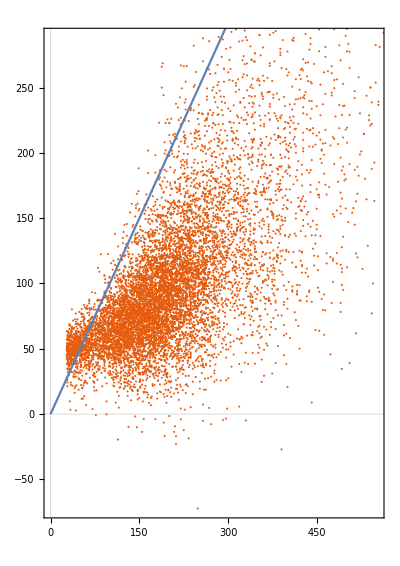

EYrainbow_1nmpp1_1st, Null Organelles filled with 0:

a[i]: {1.35383,0.895031,0.010772,0.93278,4.50069,-4.00156}

b[i,j]: (b$7889[1,1] | -0.0130187 | -0.0000369418 | -0.045353 | 0.118343 | -0.0121475
b$7889[2,1] | b$7889[2,2] | -9.70274×10^-8 | 0.00916101 | -0.011858 | -0.00106126
b$7889[3,1] | b$7889[3,2] | b$7889[3,3] | 0.0000210028 | -0.0000573007 | -0.0000583569
b$7889[4,1] | b$7889[4,2] | b$7889[4,3] | b$7889[4,4] | -0.154453 | 0.306154
b$7889[5,1] | b$7889[5,2] | b$7889[5,3] | b$7889[5,4] | b$7889[5,5] | 0.00317923
b$7889[6,1] | b$7889[6,2] | b$7889[6,3] | b$7889[6,4] | b$7889[6,5] | b$7889[6,6])

c: 18.0136

alpha[i]: {0.69029,1.25182,2.46067,0.297652,0.756884,1.42732}

Adjusted R Square: 0.971855

p-values for parameter z-statistics: {0.0575489,0.0000175937,0.00109341,0.0827488,1.57306×10^-90,4.56194×10^-17,0.0454119,0.256448,0.448039,0.0000439038,0.77817,0.95966,0.108349,0.00611051,0.806644,0.454729,0.00141141,0.0384308,3.93259×10^-8,9.01872×10^-15,0.865822,3.83904×10^-9,1.17213×10^-41,1.19479×10^-95,3.01961×10^-200,0.00344347,0.,3.39779×10^-59}

t-statistics for parameter estimates: {1.89948,4.29689,3.2669,1.73524,20.5233,-8.42247,-2.00123,-1.13493,-0.758738,4.08892,-0.281718,-0.0505823,1.6059,-2.74276,-0.244769,0.747602,-3.19379,-2.07068,-5.50097,7.77209,0.168975,5.89973,13.6251,21.1288,31.373,2.92626,83.2517,16.4039}

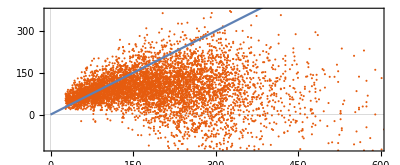

EYrainbow_leucine_large, Null Organelles filled with 0:

a[i]: {4.74747,0.0300866,2.14756,2.09294,-0.43913,-2.59391}

b[i,j]: (b$8027[1,1] | 0.000528761 | -0.0309222 | 0.105527 | -0.135775 | 0.356824
b$8027[2,1] | b$8027[2,2] | -9.37263×10^-6 | 0.00023642 | -0.000178432 | -0.000415691
b$8027[3,1] | b$8027[3,2] | b$8027[3,3] | -0.000573964 | 0.0303048 | -0.0937904
b$8027[4,1] | b$8027[4,2] | b$8027[4,3] | b$8027[4,4] | -0.147657 | 0.121681
b$8027[5,1] | b$8027[5,2] | b$8027[5,3] | b$8027[5,4] | b$8027[5,5] | 0.276239
b$8027[6,1] | b$8027[6,2] | b$8027[6,3] | b$8027[6,4] | b$8027[6,5] | b$8027[6,6])

c: 12.3106

alpha[i]: {1.24914,1.58184,1.18872,0.130618,0.814796,1.27764}

Adjusted R Square: 0.968589

p-values for parameter z-statistics: {1.54759×10^-8,0.000158917,0.000775627,7.18411×10^-7,0.302935,0.0324913,0.00232493,0.0248199,0.0203001,7.04021×10^-7,0.000111473,0.413799,0.00919273,0.00298718,0.00176219,0.918122,0.0264774,0.00825009,4.09365×10^-16,0.0220016,5.87396×10^-18,0.0165406,1.0369×10^-15,1.60555×10^-270,1.49203×10^-53,0.0728028,0.,7.00889×10^-32}

t-statistics for parameter estimates: {5.66402,3.77912,3.36308,4.96163,-1.03025,-2.13881,3.04655,-2.24476,2.32137,-4.96557,3.86674,-0.817284,2.60565,-2.97028,-3.12905,-0.102804,2.21969,-2.64254,-8.1587,2.29094,8.66237,2.39744,8.04442,37.0402,15.561,1.79438,104.098,11.8194}

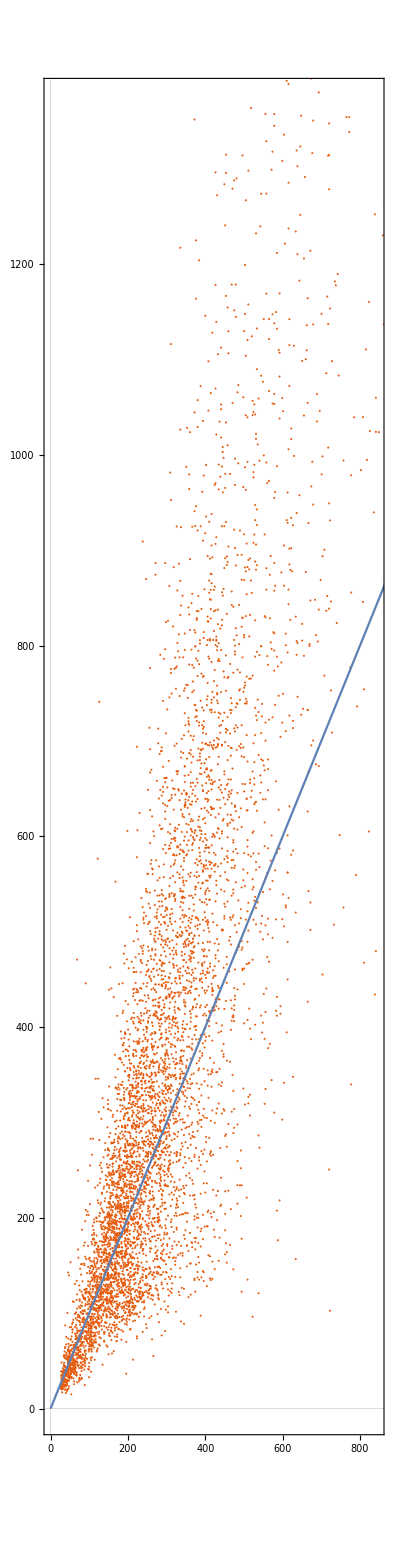

EYrainbowWhi5Up_betaEstrodiol, Null Organelles filled with 0:

a[i]: {12.106,0.0845389,1.55923,-7.55762,12.9478,-16.1061}

b[i,j]: (b$8165[1,1] | -0.00210892 | 0.0443686 | -0.162705 | 0.100668 | -0.434281
b$8165[2,1] | b$8165[2,2] | -0.0000960308 | 0.00137258 | 0.000417528 | 0.000628599
b$8165[3,1] | b$8165[3,2] | b$8165[3,3] | 0.122781 | -0.0898402 | 0.0665143
b$8165[4,1] | b$8165[4,2] | b$8165[4,3] | b$8165[4,4] | -0.0787673 | -0.19798
b$8165[5,1] | b$8165[5,2] | b$8165[5,3] | b$8165[5,4] | b$8165[5,5] | 0.336742
b$8165[6,1] | b$8165[6,2] | b$8165[6,3] | b$8165[6,4] | b$8165[6,5] | b$8165[6,6])

c: -47.615

alpha[i]: {0.919734,1.49619,1.16733,0.4949,0.762509,1.03383}

Adjusted R Square: 0.961277

p-values for parameter z-statistics: {7.55208×10^-7,0.0374871,0.226763,0.014959,8.74764×10^-8,1.70699×10^-8,0.0498375,0.460012,0.41569,0.0058755,0.00481603,0.48758,0.134661,0.149153,0.0875092,0.39245,0.340383,0.420422,0.562932,0.30092,0.0234291,0.00773737,5.38313×10^-51,4.23392×10^-71,9.88646×10^-8,0.0199457,6.26172×10^-188,8.81226×10^-11}

t-statistics for parameter estimates: {4.97905,2.08326,1.2095,-2.43769,5.39187,-5.68707,-1.96379,0.739119,-0.814268,2.76072,-2.82556,-0.694427,1.49721,1.44367,1.7104,0.855563,-0.953876,0.80603,-0.578691,-1.03501,2.26993,-2.66885,15.9364,19.3894,5.36919,2.3312,36.9923,6.55827}

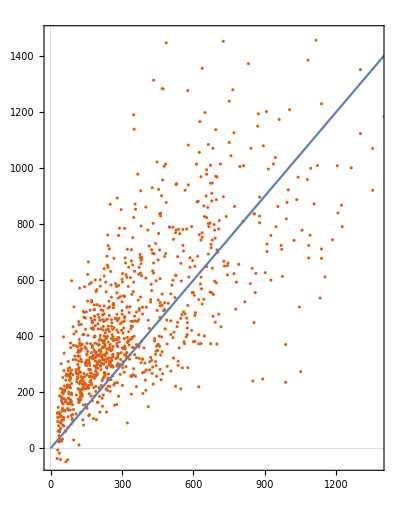

```mathematica
Do[
Print[experiments[[i]],", Null Organelles filled with 0:"];
fitCellSizeFromOrganelles[Select[filled,#[[1]]==experiments[[i]]&]];,
{i,1,Length[experiments]}
];
```

EYrainbow_glucose, Null Organelles Excluded:

a[i]: {6.3196,0.316155,0.252434,0.944634,-0.00943759,0.175869}

b[i,j]: (b$8632[1,1] | -0.000256905 | -0.00304458 | 0.0130287 | -0.000484938 | 0.111297
b$8632[2,1] | b$8632[2,2] | -0.0000856186 | 0.00100695 | -6.16329×10^-6 | -0.00221553
b$8632[3,1] | b$8632[3,2] | b$8632[3,3] | 0.00277741 | 0.000010159 | -0.000664366
b$8632[4,1] | b$8632[4,2] | b$8632[4,3] | b$8632[4,4] | -0.000396582 | -0.153746
b$8632[5,1] | b$8632[5,2] | b$8632[5,3] | b$8632[5,4] | b$8632[5,5] | 0.00037071
b$8632[6,1] | b$8632[6,2] | b$8632[6,3] | b$8632[6,4] | b$8632[6,5] | b$8632[6,6])

c: 34.5562

alpha[i]: {0.812447,1.29339,1.84135,0.204561,1.89087,0.229374}

Adjusted R Square: 0.939031

p-values for parameter z-statistics: {2.53243×10^-9,2.76181×10^-6,0.0101533,0.222582,0.432661,0.79444,0.803923,0.0484024,0.885893,0.460602,0.177168,0.0310798,0.212095,0.457224,0.0279802,0.0898915,0.487444,0.46253,0.473551,0.0217046,0.457855,3.25396×10^-8,5.79013×10^-22,2.23774×10^-201,1.5034×10^-68,0.282208,1.139×10^-12,0.278907}

t-statistics for parameter estimates: {5.97443,4.69524,2.57192,1.2199,-0.784734,0.260569,-0.248291,-1.97449,0.143513,-0.737934,1.34979,-2.15689,1.24805,-0.743506,-2.19845,1.69642,0.694452,-0.734765,-0.716788,-2.29649,0.742464,5.53927,9.69601,32.3048,17.8755,1.07553,7.13802,1.08294}

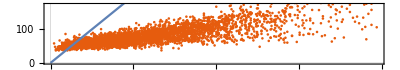

EYrainbow_glucose_largerBF, Null Organelles Excluded:

a[i]: {6.82819,0.215318,0.0648138,2.21496,4.13243,-4.10368}

b[i,j]: (b$8770[1,1] | -0.0029774 | -0.0014265 | 0.164387 | 0.159232 | -0.302679
b$8770[2,1] | b$8770[2,2] | -0.0000591979 | 0.00230451 | -0.00194773 | 0.000943707
b$8770[3,1] | b$8770[3,2] | b$8770[3,3] | 0.0098963 | -0.00119951 | 0.000931009
b$8770[4,1] | b$8770[4,2] | b$8770[4,3] | b$8770[4,4] | 0.0271166 | -0.216819
b$8770[5,1] | b$8770[5,2] | b$8770[5,3] | b$8770[5,4] | b$8770[5,5] | 0.0712457
b$8770[6,1] | b$8770[6,2] | b$8770[6,3] | b$8770[6,4] | b$8770[6,5] | b$8770[6,6])

c: 33.2388

alpha[i]: {1.27374,1.48705,1.73785,0.846453,0.778396,0.402141}

Adjusted R Square: 0.952294

p-values for parameter z-statistics: {0.000082931,0.0000188967,0.0857354,0.0358257,9.38213×10^-30,3.89388×10^-16,0.00440274,0.617854,0.196921,0.0137652,0.000013296,0.346224,0.00576443,0.0000908945,0.00770451,0.360358,0.25475,0.468983,0.578416,5.76052×10^-6,3.25937×10^-10,5.63551×10^-6,5.8414×10^-55,1.54124×10^-171,3.00485×10^-13,3.42971×10^-28,0.,2.0404×10^-52}

t-statistics for parameter estimates: {3.93931,4.28205,1.71871,2.09952,11.4098,-8.17178,-2.84918,-0.498928,1.29056,2.46428,-4.35992,-0.942037,2.76219,-3.91718,2.66593,0.914775,-1.13903,0.724196,0.555739,-4.54033,6.29982,4.54498,15.8248,29.1509,7.31579,11.0835,79.5807,15.4317}

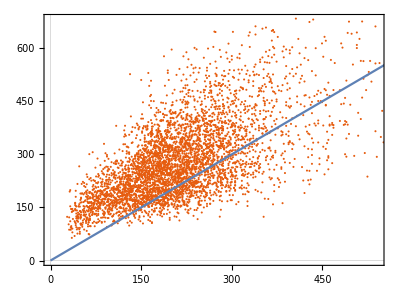

EYrainbow_rapamycin_1stTry, Null Organelles Excluded:

a[i]: {4.14411,0.0151606,0.107653,-3.59949,3.80154,-4.44978}

b[i,j]: (b$8916[1,1] | -0.000299597 | -0.000230678 | -0.137095 | 0.0648808 | -0.0287444
b$8916[2,1] | b$8916[2,2] | 2.58892×10^-7 | 0.000327561 | -0.000214523 | 0.0000409419
b$8916[3,1] | b$8916[3,2] | b$8916[3,3] | 0.000773329 | 0.000231008 | -0.000930741
b$8916[4,1] | b$8916[4,2] | b$8916[4,3] | b$8916[4,4] | -0.0421119 | 0.0937011
b$8916[5,1] | b$8916[5,2] | b$8916[5,3] | b$8916[5,4] | b$8916[5,5] | 0.101406
b$8916[6,1] | b$8916[6,2] | b$8916[6,3] | b$8916[6,4] | b$8916[6,5] | b$8916[6,6])

c: 59.0319

alpha[i]: {0.469907,1.87639,1.84197,1.88972,0.769455,0.630096}

Adjusted R Square: 0.968734

p-values for parameter z-statistics: {8.19544×10^-6,0.0298722,0.0037815,0.0000359578,1.27213×10^-32,6.74417×10^-14,0.0401436,0.745897,0.191569,0.160175,0.649184,0.468999,0.0402852,0.0379749,0.387399,0.219935,0.385642,0.0641315,0.294845,0.0845495,2.33291×10^-7,1.58602×10^-35,6.93898×10^-13,9.8902×10^-88,2.63107×10^-101,7.78738×10^-21,0.,9.88165×10^-11}

t-statistics for parameter estimates: {4.46523,2.17247,2.89736,-4.1362,11.9893,-7.51675,-2.05287,-0.324075,-1.30615,1.40472,-0.454926,0.724171,2.05141,-2.07574,0.864428,1.22687,0.867633,-1.85172,-1.04768,1.72526,5.17867,12.549,7.20178,20.3023,21.9268,9.40908,79.1882,6.48427}

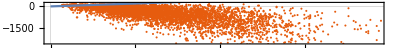

EYrainbow_rapamycin_CheckBistability, Null Organelles Excluded:

a[i]: {3.22976,1.0393,0.122677,2.16553,0.640097,-1.27546}

b[i,j]: (b$9062[1,1] | 0.00510531 | 0.000752387 | -0.0256533 | 0.0236889 | -0.0368686
b$9062[2,1] | b$9062[2,2] | -0.000330785 | -0.000712059 | -0.000512885 | -0.0081238
b$9062[3,1] | b$9062[3,2] | b$9062[3,3] | 0.00139073 | 0.000155323 | 0.00016925
b$9062[4,1] | b$9062[4,2] | b$9062[4,3] | b$9062[4,4] | -0.0487781 | -0.00907953
b$9062[5,1] | b$9062[5,2] | b$9062[5,3] | b$9062[5,4] | b$9062[5,5] | 0.0470124
b$9062[6,1] | b$9062[6,2] | b$9062[6,3] | b$9062[6,4] | b$9062[6,5] | b$9062[6,6])

c: 44.017

alpha[i]: {0.89885,1.13373,1.81989,0.109923,0.914888,0.521854}

Adjusted R Square: 0.97296

p-values for parameter z-statistics: {1.62042×10^-11,2.76636×10^-11,0.00399452,2.79108×10^-12,0.000695732,0.000130321,0.0734404,0.315556,0.184871,0.193599,0.174893,0.0220754,0.614308,0.611534,0.00097476,0.0461138,0.493438,0.710649,4.9513×10^-6,0.548547,2.2094×10^-6,2.88091×10^-32,3.24463×10^-166,1.50155×10^-216,6.00732×10^-72,0.352899,0.,0.000392999}

t-statistics for parameter estimates: {6.74841,6.66983,2.8796,7.00093,3.39284,-3.82809,1.79037,1.00371,-1.32604,1.30014,-1.35679,-2.2896,-0.503957,-0.507909,-3.29918,1.99472,0.684889,0.371,-4.57058,-0.59997,4.73742,11.8882,28.2747,32.6083,18.1566,0.929046,41.9712,3.54654}

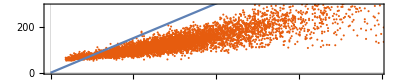

EYrainbow_1nmpp1_1st, Null Organelles Excluded:

a[i]: {2.82073,1.57771,0.00400205,0.180546,2.99271,-4.30469}

b[i,j]: (b$9200[1,1] | -0.0526544 | 0.0000322023 | 0.0467944 | -0.0209793 | 0.0520156
b$9200[2,1] | b$9200[2,2] | -1.9303×10^-6 | 0.016366 | -0.00475775 | -0.0258409
b$9200[3,1] | b$9200[3,2] | b$9200[3,3] | -0.0000260599 | -0.0000182998 | -0.0000281541
b$9200[4,1] | b$9200[4,2] | b$9200[4,3] | b$9200[4,4] | -0.0250363 | 0.107767
b$9200[5,1] | b$9200[5,2] | b$9200[5,3] | b$9200[5,4] | b$9200[5,5] | 0.0571036
b$9200[6,1] | b$9200[6,2] | b$9200[6,3] | b$9200[6,4] | b$9200[6,5] | b$9200[6,6])

c: 35.4649

alpha[i]: {0.72322,1.11896,2.70262,-0.0366288,0.803261,1.56827}

Adjusted R Square: 0.976581

p-values for parameter z-statistics: {0.00172515,4.6202×10^-6,0.0064543,0.701529,2.57011×10^-33,4.45937×10^-16,0.000126289,0.119296,0.343138,0.511385,0.251397,0.137185,0.0454353,0.438455,0.0208479,0.0473238,0.00506486,0.0421151,0.163379,0.000468873,0.000732846,2.37752×10^-15,2.89127×10^-33,9.30279×10^-94,1.47151×10^-173,0.819856,0.,5.94871×10^-39}

t-statistics for parameter estimates: {3.13575,4.58692,2.72503,0.383281,12.1245,-8.15566,-3.83692,1.55803,0.948083,-0.656735,1.14711,-1.48662,2.00116,-0.774874,-2.31154,-1.98393,-2.80426,-2.03296,-1.39402,3.5005,3.37931,7.94793,12.1145,21.0318,29.361,-0.227744,76.4054,13.1801}

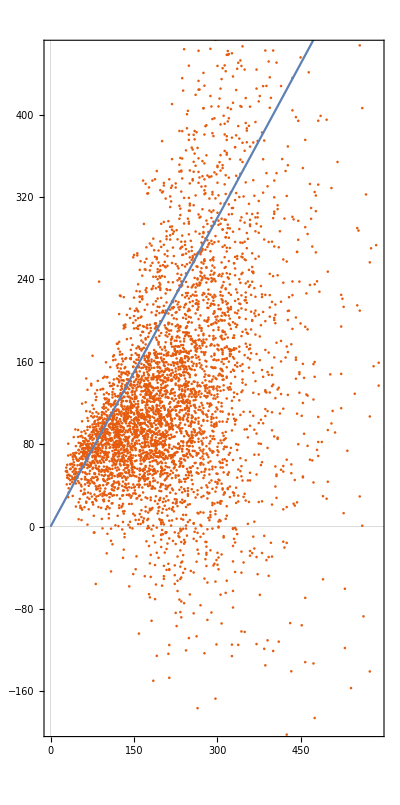

EYrainbow_leucine_large, Null Organelles Excluded:

a[i]: {6.5014,0.0336701,2.97678,1.84013,-1.47872,-0.325097}

b[i,j]: (b$9338[1,1] | 0.000654457 | -0.0565323 | 0.0700491 | -0.189782 | 0.387011
b$9338[2,1] | b$9338[2,2] | -0.0000772435 | 0.000266788 | -0.000161842 | -0.00027435
b$9338[3,1] | b$9338[3,2] | b$9338[3,3] | 0.00661489 | 0.0568028 | -0.103317
b$9338[4,1] | b$9338[4,2] | b$9338[4,3] | b$9338[4,4] | -0.124738 | -0.00380945
b$9338[5,1] | b$9338[5,2] | b$9338[5,3] | b$9338[5,4] | b$9338[5,5] | 0.199646
b$9338[6,1] | b$9338[6,2] | b$9338[6,3] | b$9338[6,4] | b$9338[6,5] | b$9338[6,6])

c: 18.007

alpha[i]: {1.23062,1.59724,1.08985,0.127126,0.800504,0.999744}

Adjusted R Square: 0.969829

p-values for parameter z-statistics: {1.70083×10^-6,0.00253323,0.0483182,0.00162777,0.0890722,0.829951,0.0144819,0.149142,0.1944,0.0000181656,0.000125469,0.216055,0.0227832,0.0204702,0.0927689,0.608548,0.190992,0.115574,3.07786×10^-7,0.943611,2.05516×10^-9,0.0400712,1.6206×10^-13,1.93912×10^-154,1.70937×10^-16,0.172217,0.,5.26194×10^-15}

t-statistics for parameter estimates: {4.79268,3.02111,1.97512,3.15287,-1.70069,-0.214777,2.44607,-1.44283,1.29787,-4.29112,3.83867,-1.23727,2.27786,-2.31847,-1.68134,0.512185,1.30786,-1.57394,-5.12667,-0.0707367,6.00619,2.05363,7.40055,27.5847,8.27381,1.36534,79.2662,7.84866}

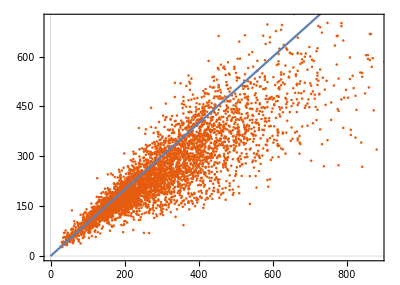

EYrainbowWhi5Up_betaEstrodiol, Null Organelles Excluded:

a[i]: {11.0457,0.226281,0.737605,-0.623217,10.4347,-8.24383}

b[i,j]: (b$9476[1,1] | -0.00278813 | -0.00960378 | -0.413423 | 0.487942 | -0.98258
b$9476[2,1] | b$9476[2,2] | -0.0000952229 | 0.00147635 | -0.00227362 | 0.00715673
b$9476[3,1] | b$9476[3,2] | b$9476[3,3] | 0.129065 | -0.0335371 | 0.102256
b$9476[4,1] | b$9476[4,2] | b$9476[4,3] | b$9476[4,4] | -0.595446 | 0.328885
b$9476[5,1] | b$9476[5,2] | b$9476[5,3] | b$9476[5,4] | b$9476[5,5] | -0.0734471
b$9476[6,1] | b$9476[6,2] | b$9476[6,3] | b$9476[6,4] | b$9476[6,5] | b$9476[6,6])

c: -55.356

alpha[i]: {0.893499,1.31743,1.24987,0.883607,0.744186,1.12757}

Adjusted R Square: 0.961843

p-values for parameter z-statistics: {2.60904×10^-6,0.0635114,0.150454,0.88596,5.1747×10^-7,0.02952,0.113441,0.690404,0.111504,2.0461×10^-6,4.14954×10^-6,0.645742,0.482943,0.197954,0.115325,0.396614,0.35521,0.388573,0.0210105,0.272646,0.6877,0.00198911,2.98132×10^-48,2.00365×10^-43,1.52421×10^-8,0.000653526,2.19823×10^-144,5.58067×10^-14}

t-statistics for parameter estimates: {4.73038,1.85794,1.43918,-0.143459,5.05728,-2.18002,-1.58449,-0.398437,-1.59307,4.78074,-4.6329,-0.459844,0.701875,-1.28837,1.57626,0.848098,-0.925018,0.862635,-2.31195,1.09768,-0.402111,-3.10114,15.5293,14.6054,5.71227,3.42061,31.1753,7.64197}

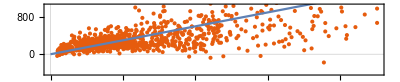

```mathematica
Do[
Print[experiments[[i]],", Null Organelles Excluded:"];
fitCellSizeFromOrganelles[Select[washed,#[[1]]==experiments[[i]]&]];,
{i,1,Length[experiments]}
]
```